# Relaciones de Kramers Kronig

```mathematica
(*En este código se definen las funciones para obtener la parte real o la parte imaginaria del índice de refracción empleando las relaciones de Kramers-Kronig. Además, se añade una función para estimar de manera autoconsistente las partes reales e imaginarias del índice de refracción*)
```

```mathematica
(*La siguiente función calcula la parte imaginaria del índice de refracción k a partir de la parte real n, usando la relación KK*)
(*Entradas: tienen que ser listas de puntos
  omega-vector de frecuencias (debe estar equiespaciado)
nreal-vector de la parte real del índice de refracción
 Salida:
  kimag-vector estimado de la parte imaginaria del índice de refracción*)
```

```mathematica
kkimrefractiveindex[omega_,nreal_]:=Module[{g=Length[omega],
									kimag = ConstantArray[0,Length[nreal]],
									(*a y b son vectores para acumular los puntos*)
									a=ConstantArray[0,Length[nreal]], 
									b=ConstantArray[0,Length[nreal]],
									deltaomega=omega[[2]]-omega[[1]],k,j},
									(*Asegurarse de que sean vectores fila*)
									If[MatrixQ[omega]&&Dimensions[omega][[1]]>Dimensions[omega][[2]],   omega=Transpose[omega]];
									(*Primer punto, excluye omega[[1]]*)

									For[k=2,k<=g,k++,b[[1]] =b[[1]]  + (nreal[[k]]-1) / (omega[[k]]^2 - omega[[1]]^2)];
									kimag[[1]]=-2*omega[[1]]/Pi*deltaomega*b[[1]];
									(*último punto, excluye omega[[g]]*)

									For[k=1,k<=g-1,k++,a[[g]] =a[[g]]  + (nreal[[k]]-1) / (omega[[k]]^2 - omega[[g]]^2)];
									kimag[[g]]=-2*(omega[[g]]/Pi)*(deltaomega*a[[g]]);
									(*Puntos intermedios*)
									For[j=2,j<=g-1,j++,
									For[k=1,k<=j-1,k++,a[[j]] =a[[j]]  + (nreal[[k]]-1) / (omega[[k]]^2 - omega[[j]]^2)];
									For[k=j+1,k<=g,k++,b[[j]] =b[[j]]  + (nreal[[k]]-1) / (omega[[k]]^2 - omega[[j]]^2)];
									kimag[[j]]=-2*omega[[j]]/Pi*deltaomega*(a[[j]]+b[[j]])];
									kimag]
```

```mathematica
(*La siguiente función calcula la parte real del índice de refracción n a partir de la parte imaginaria k, usando la relación KK*)
(*Entradas: tienen que ser listas de puntos
  omega-vector de frecuencias (debe estar equiespaciado)
kimag-vector de la parte imaginaria del índice de refracción
 Salida:
  nreal-vector estimado de la parte real del índice de refracción*)
```

```mathematica
kkrerefractiveindex[omega_,kimag_]:=Module[{g=Length[omega],
									nreal = ConstantArray[0,Length[kimag]],
									(*a y b son vectores para acumular los puntos*)
									a=ConstantArray[0,Length[kimag]], 
									b=ConstantArray[0,Length[kimag]],
									deltaomega=omega[[2]]-omega[[1]],k,j},
									(*Asegurarse de que sean vectores fila*)
									If[MatrixQ[omega]&&Dimensions[omega][[1]]>Dimensions[omega][[2]],   omega=Transpose[omega]];
									(*Primer punto, excluye omega[[1]]*)

									For[k=2,k<=g,k++,b[[1]] =b[[1]]  + (kimag[[k]]*omega[[k]]) / (omega[[k]]^2 - omega[[1]]^2)];
									nreal[[1]]=(2/Pi*deltaomega*b[[1]])+1;
									(*último punto, excluye omega[[g]]*)

									For[k=1,k<=g-1,k++,a[[g]] =a[[g]]  + (kimag[[k]]*omega[[k]]) / (omega[[k]]^2 - omega[[g]]^2)];
									nreal[[g]]=(2/Pi*(deltaomega*a[[g]]))+1;
									(*Puntos intermedios*)
									For[j=2,j<=g-1,j++,
									For[k=1,k<=j-1,k++,a[[j]] =a[[j]]  + (kimag[[k]]*omega[[k]]) / (omega[[k]]^2 - omega[[j]]^2)];
									For[k=j+1,k<=g,k++,b[[j]] =b[[j]]  + (kimag[[k]]*omega[[k]]) / (omega[[k]]^2 - omega[[j]]^2)];
									nreal[[j]]=(2/Pi*deltaomega*(a[[j]]+b[[j]]))+1];
									nreal]
```

```mathematica
(*La siguiente función hace una estimación auto-consistente del índice de refracción complejo utilizando las relaciones de Kramers-Kronig.
Entradas:
omega-vector de frecuencias
reN-vector de la parte real inicial (estimación o medida)
	imN-vector de la parte imaginaria inicial (estimación o medida)
	 N-número de iteraciones del proceso auto-consistente
	mu-factor de mezcla entre el valor inicial y el nuevo (0<mu<1)
Salidas:% refin-parte real auto-consistente de la susceptibilidad
	imfin-parte imaginaria auto-consistente de la susceptibilidad *)
```

```mathematica
selfconsrefractiveindex[omega_,n_,k_,N_,mu_]:=Module[{comodo1,comodo2,refin,imfin,j},
							(*Asegurarse de que los valores sean útiles*)
												If[MatrixQ[omega]&&Dimensions[omega][[1]]>Dimensions[omega][[2]],   omega=Transpose[omega]];
If[MatrixQ[n]&&Dimensions[n][[1]]>Dimensions[n][[2]],   n=Transpose[n]];
If[MatrixQ[k]&&Dimensions[k][[1]]>Dimensions[k][[2]],   k=Transpose[k]];
(*Inicializa variables auxiliares*)
comodo1=n;(* Estimación de la parte real*)
comodo2=k;(* Estimación de la parte imaginaria*)
(*Bucle autoconsistente*)
For[j=1,j<=N,j++,
(*Calcula nueva parte real a partir de k anterior*)
comodo1=kkrerefractiveindex[omega,comodo2];
(*Mezcla con la estimación inicial*)
comodo1=mu*n+(1-mu)*comodo1;
(*Calcula nueva parte imaginaria a partir de n actualizada*)
comodo2=kkimrefractiveindex[omega,comodo1];
(* Mezcla con la estimación inicial*)
comodo2=mu*k+(1-mu)*comodo2;
];
refin=comodo1;
imfin=comodo2;
{refin,imfin}]
```

```mathematica
a=ConstantArray[0,Dimensions[nreal]]
```

{0,0,0,0}

```mathematica
a[[g]]
```

0

```mathematica
orok=kkimrefractiveindex[omegaAu,nInterpAu];
oron=kkrerefractiveindex[omegaAu,kInterpAu];
```

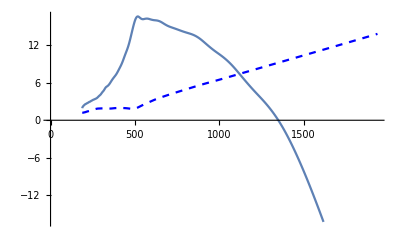

```mathematica
ListLinePlot[{Transpose[{lambdaInterpAu,orok}],Style[Transpose[{lambdaInterpAu,kInterpAu}],Blue,Dashed]}]
```

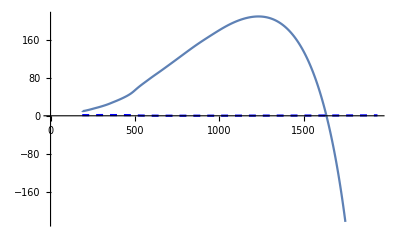

```mathematica
ListLinePlot[{Transpose[{lambdaInterpAu,oron}],Style[Transpose[{lambdaInterpAu,nInterpAu}],Blue,Dashed]}]
```

```mathematica
orobueno=selfconsrefractiveindex[omegaAu,nInterpAu,kInterpAu,50,1];
```

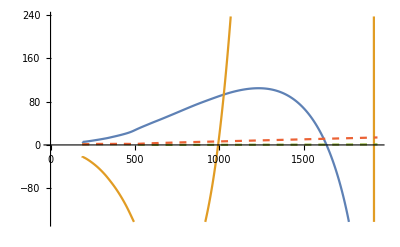

```mathematica
ListLinePlot[{Transpose[{lambdaInterpAu,orobueno[[1]]}],Style[Transpose[{lambdaInterpAu,orobueno[[2]]}]],Style[Transpose[{lambdaInterpAu,nInterpAu}],Dashed],Style[Transpose[{lambdaInterpAu,kInterpAu}],Dashed]}]
```

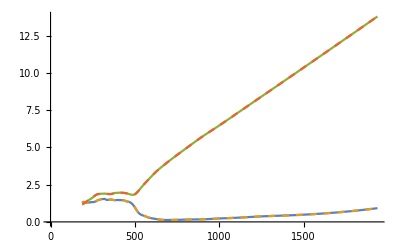

```mathematica
ListLinePlot[{Transpose[{lambdaInterpAu,orobueno[[1]]}],Style[Transpose[{lambdaInterpAu,nInterpAu}],Dashed],Transpose[{lambdaInterpAu,orobueno[[2]]}],Style[Transpose[{lambdaInterpAu,kInterpAu}],Dashed]}]
```